```mathematica
u[x_,y_,t_,d_]:=1/(4*Pi*t*Sqrt[Det[d]])*Exp[-(Transpose[{x,y}].Inverse[d].{x,y})/(4*t)];
d10={{0.489794,-0.086213},{-0.086213,0.016206}};
d45={{0.253,-0.252},{-0.252,0.253}};
d22={{0.431191,-0.178191},{-0.178191,0.074809}};
(*d5={{0.5,-0.045},{-0.045,0.005}};*)
dAll={d10,d22,d45,d5};
```

```mathematica
basePath="C:\\Users\\Maria\\Desktop\\Svf\\5rocnik\\NADR\\build\\";
methodsDCM={"DCM_Classic","S1_FBDS_Classic","S2_FBDS_Classic"};
methodsADCM={"ADCM_Modified","S1_FBDS_ADCM","S2_FBDS_ADCM"};
Ns={20,40,80,160};
(*thetasIMPORT={10,22,45,5};*)
(*thetas={10,22.5,45,5};*)
thetasIMPORT={10,22,45};
thetas={10,22.5,45};
```

```mathematica
yFixed={0.025,0.0125,0.00625,0.003125};
rowFixed={11,21,41,81};
colors={Blue,Green,Orange,Purple};
xValsAll=Table[h=2./Ns[[n]];
Table[-1+h/2+j*h,{j,0,Ns[[n]]-1}],{n,1,Length[Ns]}];
```

```mathematica
exactPlot[y_,d_]:=Plot[u[x,y,0.3,d],{x,-1,1},PlotRange->All,PlotStyle->Red];
```

```mathematica
importData[methods_]:=Table[raw=Import[basePath<>methods[[m]]<>"\\final_N"<>ToString[Ns[[n]]]<>"_theta"<>ToString[thetasIMPORT[[t]]]<>".csv"];
raw[[2;;-2,2;;-2]],{m,1,Length[methods]},{n,1,Length[Ns]},{t,1,Length[thetasIMPORT]}];

dataDCM=importData[methodsDCM];
dataADCM=importData[methodsADCM];
```

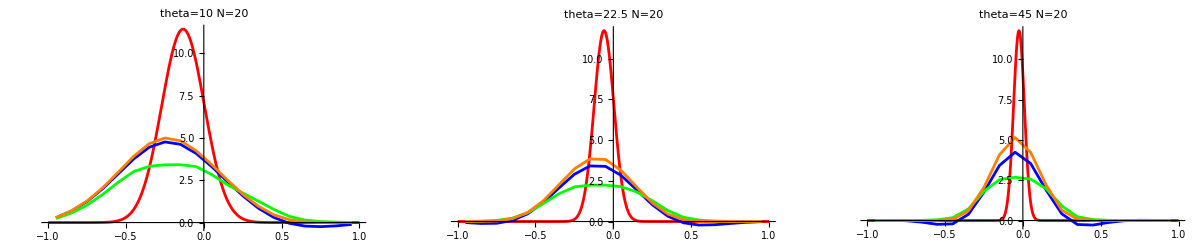

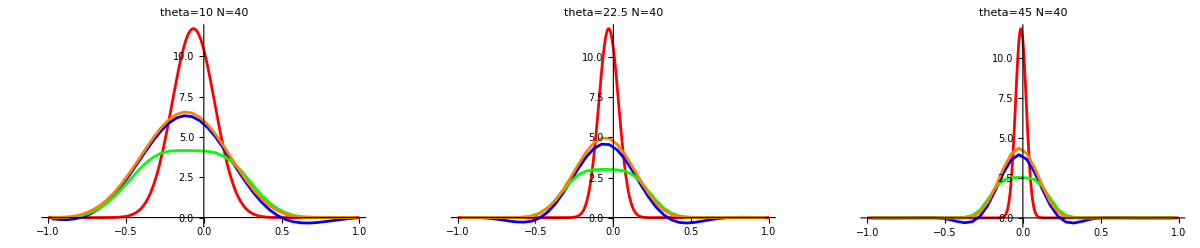

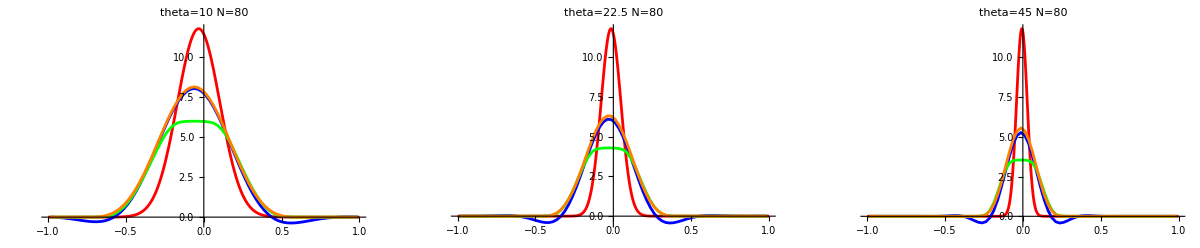

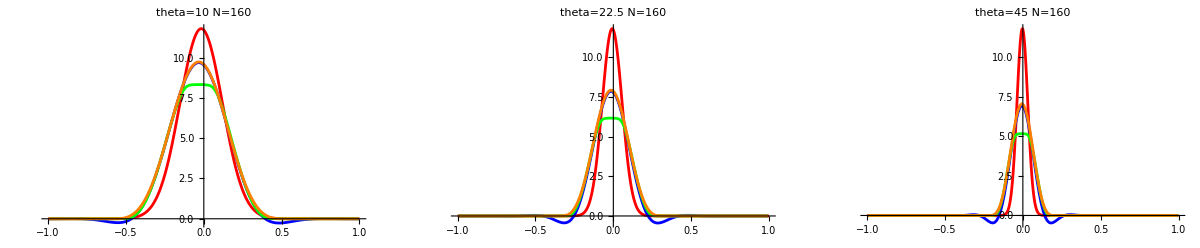

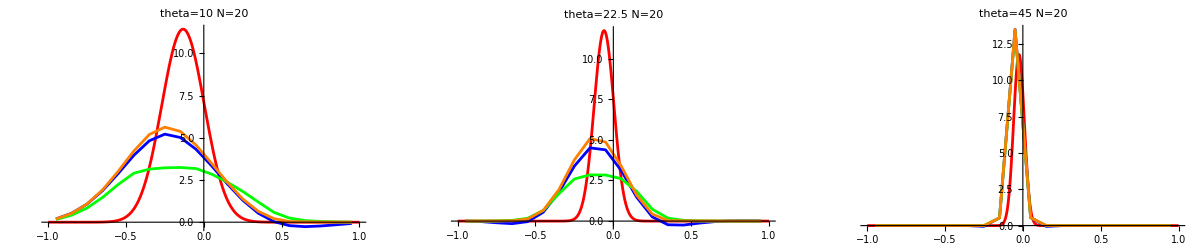

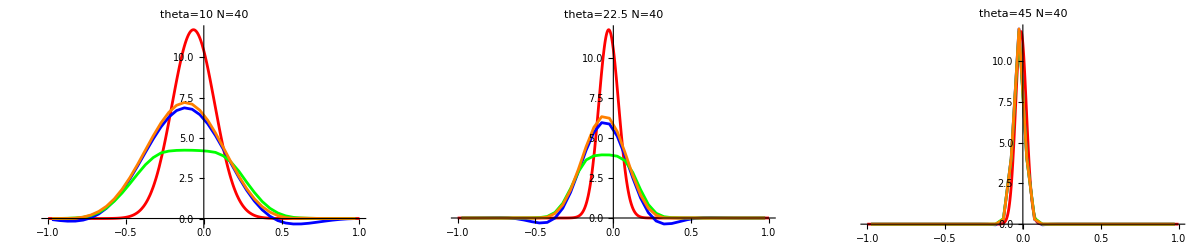

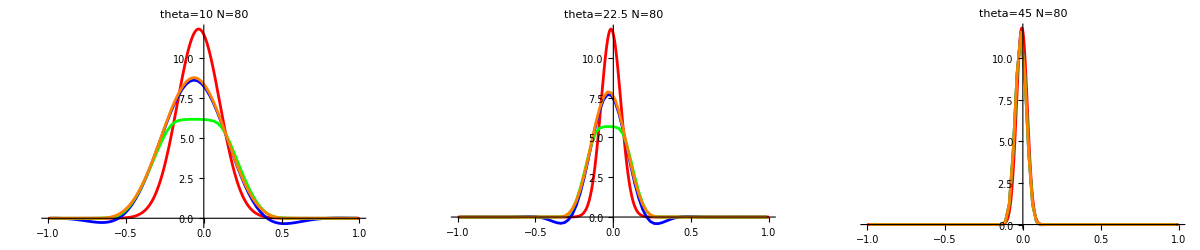

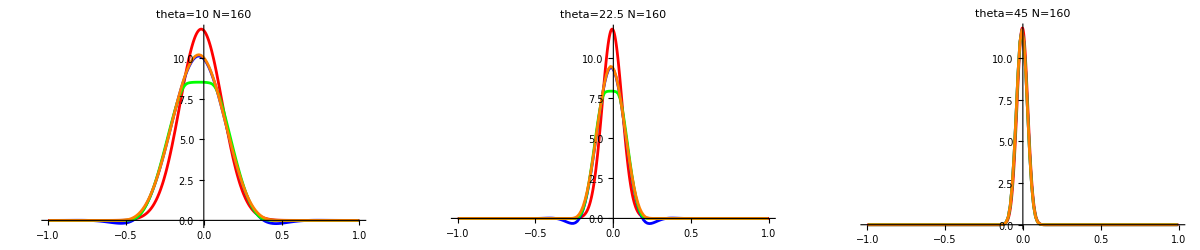

```mathematica
makeCrossSections[data_,methods_]:=Table[Show[exactPlot[yFixed[[n]],dAll[[t]]],Table[ListLinePlot[Transpose[{xValsAll[[n]],data[[m,n,t,rowFixed[[n]],All]]}],PlotStyle->colors[[m]],PlotRange->All],{m,1,Length[methods]}],PlotLabel->Row[{"theta=",thetas[[t]]," N=",Ns[[n]]}]],{n,1,Length[Ns]},{t,1,Length[thetas]}];

crossDCM=makeCrossSections[dataDCM,methodsDCM];
crossADCM=makeCrossSections[dataADCM,methodsADCM];

legendDCM=LineLegend[Join[{Red},colors],Join[{"exact"},methodsDCM]];
legendADCM=LineLegend[Join[{Red},colors],Join[{"exact"},methodsADCM]];

Do[Print[Legended[GraphicsGrid[{crossDCM[[n]]}],Placed[legendDCM,Right]]],{n,1,Length[Ns]}]

Do[Print[Legended[GraphicsGrid[{crossADCM[[n]]}],Placed[legendADCM,Right]]],{n,1,Length[Ns]}]
```

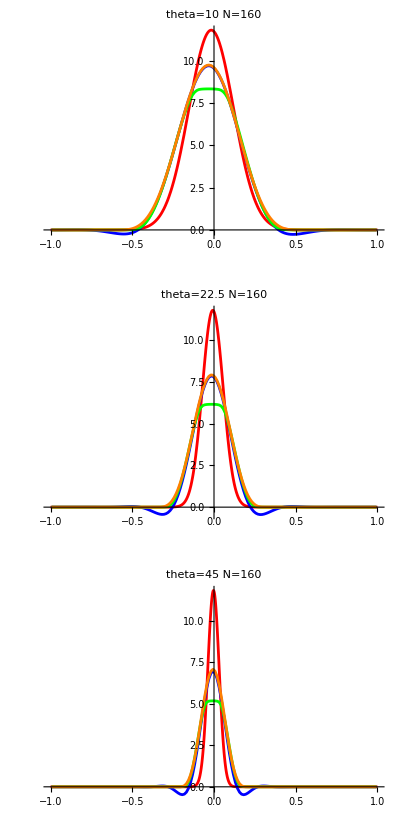

```mathematica
Legended[GraphicsGrid[Partition[crossDCM[[4]],1]],Placed[legendDCM,Right]]
```

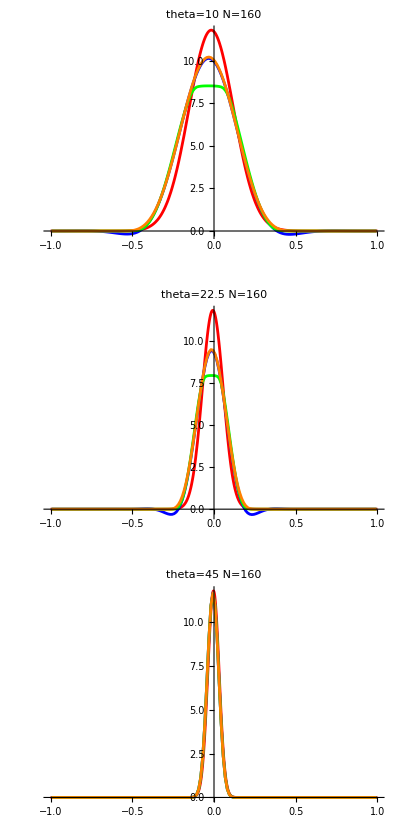

```mathematica
Legended[GraphicsGrid[Partition[crossADCM[[4]],1]],Placed[legendADCM,Right]]
```